# Obligate mutualistic cooperation limits evolvability

## Clustering Analysis

```mathematica
profiles=Import["/Users/xxxx.xlsx"];
```

## Ampicillin

```mathematica
nez[x_]:=If[x<0.005,0,x]
```

```mathematica
coAmp1=Table[nez/@(profiles[[2]][[i]][[#]]&/@Range[9,45,3]),{i,3,42}];
```

```mathematica
coAmp2=Table[nez/@(profiles[[2]][[i]][[#]]&/@Range[10,46,3]),{i,3,42}];
```

```mathematica
coAmp=Join[coAmp1,coAmp2];
```

```mathematica
tyrAmp1=Table[nez/@(profiles[[4]][[i]][[#]]&/@Range[9,45,3]),{i,3,42}];
tyrAmp2=Table[nez/@(profiles[[4]][[i]][[#]]&/@Range[10,46,3]),{i,3,42}];
tyrAmp=Join[tyrAmp1,tyrAmp2];
```

```mathematica
colorCoAmp=RGBColor[214/255,49/255,255/255];
```

```mathematica
colorTRPAmp=RGBColor[253/255,13/255,0/255];
```

```mathematica
colorTYRAmp=RGBColor[5/255,38/255,255/255];
```

```mathematica
dat1Amp=(#[[1]]-> #[[2]]&)/@Partition[Riffle[coAmp,Table[colorCoAmp,{80}]],{2}];
```

```mathematica
dat2Amp=(#[[1]]-> #[[2]]&)/@Partition[Riffle[trpAmp,Table[colorTRPAmp,{80}]],{2}];
```

```mathematica
dat3Amp=(#[[1]]-> #[[2]]&)/@Partition[Riffle[tyrAmp,Table[colorTYRAmp,{80}]],{2}];
```

```mathematica
datAmp=Join[dat1Amp,dat2Amp,dat3Amp];
```

```mathematica
ClusteringTree[datAmp,GraphLayout->"RadialEmbedding", ClusterDissimilarityFunction->"Average",ImageSize->500]
```

```mathematica
DeleteDuplicates[Flatten@Trace[FindClusters[(#[[1]]&/@datAmp),Method->Automatic],HoldPattern[Rule["Method",_]],TraceInternal->True]]
```

{Method→DBSCAN}

```mathematica
ClusteringTree[datAmp,GraphLayout->"RadialEmbedding", ClusterDissimilarityFunction->"Average",ImageSize->500]
FindClusters[datAmp]
Length[FindClusters[datAmp]]
Length/@FindClusters[datAmp]
```

3

{80,82,78}

```mathematica
DeleteDuplicates[Flatten@Trace[FindClusters[(Flatten[afMIC[#,5]&/@datAmp,1]),Method->Automatic],HoldPattern[Rule["Method",_]],TraceInternal->True]]
```

{Method→NeighborhoodContraction}

```mathematica
ClusteringTree[Flatten[afMIC[#,5]&/@datAmp,1],GraphLayout->"RadialEmbedding", ClusterDissimilarityFunction->"Average",ImageSize->500]
```

```mathematica
FindClusters[Flatten[afMIC[#,5]&/@datAmp,1]]
Length[FindClusters[Flatten[afMIC[#,5]&/@datAmp,1]]]
Length/@FindClusters[Flatten[afMIC[#,5]&/@datAmp,1]]
```

3

{80,80,80}

## Kanamycin

```mathematica
nez[x_]:=If[x<0.005,0,x]
```

```mathematica
coKana1=Table[nez/@(profiles[[2]][[i]][[#]]&/@Range[9,45,3]),{i,93,132}];
```

```mathematica
coKana2=Table[nez/@(profiles[[2]][[i]][[#]]&/@Range[10,46,3]),{i,93,132}];
```

```mathematica
coKana=Join[coKana1,coKana2];
```

```mathematica
trpKana1=Table[nez/@(profiles[[3]][[i]][[#]]&/@Range[9,45,3]),{i,93,132}];
```

```mathematica
trpKana2=Table[nez/@(profiles[[3]][[i]][[#]]&/@Range[10,46,3]),{i,93,132}];
```

```mathematica
trpKana=Join[trpKana1,trpKana2];
```

```mathematica
tyrKana1=Table[nez/@(profiles[[4]][[i]][[#]]&/@Range[9,45,3]),{i,93,132}];
tyrKana2=Table[nez/@(profiles[[4]][[i]][[#]]&/@Range[10,46,3]),{i,93,132}];
tyrKana=Join[tyrKana1,tyrKana2];
```

```mathematica
colorCoKana=RGBColor[214/255,49/255,255/255];
```

```mathematica
colorTRPKana=RGBColor[253/255,13/255,0/255];
```

```mathematica
colorTYRKana=RGBColor[5/255,38/255,255/255];
```

```mathematica
dat1Kana=(#[[1]]-> #[[2]]&)/@Partition[Riffle[coKana,Table[colorCoKana,{80}]],{2}];
```

```mathematica
dat2Kana=(#[[1]]-> #[[2]]&)/@Partition[Riffle[trpKana,Table[colorTRPKana,{80}]],{2}];
```

```mathematica
dat3Kana=(#[[1]]-> #[[2]]&)/@Partition[Riffle[tyrKana,Table[colorTYRKana,{80}]],{2}];
```

```mathematica
datKana=Join[dat1Kana,dat2Kana,dat3Kana];
```

```mathematica
ClusteringTree[datKana,GraphLayout->"RadialEmbedding", ClusterDissimilarityFunction->"Average",ImageSize->500]
```

```mathematica
FindClusters[datKana]
Length[FindClusters[#[[1]]&/@datKana]]
Length/@FindClusters[#[[1]]&/@datKana]
```

3

{141,72,27}

```mathematica
DeleteDuplicates[Flatten@Trace[FindClusters[datKana,Method->Automatic],HoldPattern[Rule["Method",_]],TraceInternal->True]]
```

{Method→DBSCAN}

```mathematica
ClusteringTree[Flatten[afMIC[#,5]&/@datKana,1],GraphLayout->"RadialEmbedding", ClusterDissimilarityFunction->"Average",ImageSize->500]
FindClusters[Flatten[afMIC[#,5]&/@datKana,1]]
Length[FindClusters[Flatten[afMIC[#,5]&/@datKana,1]]]
Length/@FindClusters[Flatten[afMIC[#,5]&/@datKana,1]]
```

2

{80,160}

```mathematica
DeleteDuplicates[Flatten@Trace[FindClusters[Flatten[afMIC[#,5]&/@datKana,1],Method->Automatic],HoldPattern[Rule["Method",_]],TraceInternal->True]]
```

{Method→NeighborhoodContraction}

```mathematica
FindClusters[Flatten[afMIC[#,-8]&/@datKana,1]]
Length[FindClusters[Flatten[afMIC[#,-8]&/@datKana,1]]]
Length/@FindClusters[Flatten[afMIC[#,-8]&/@datKana,1]]
```

2

{142,98}

```mathematica
DeleteDuplicates[Flatten@Trace[FindClusters[Flatten[afMIC[#,-8]&/@datKana,1],Method->Automatic],HoldPattern[Rule["Method",_]],TraceInternal->True]]
```

{Method→DBSCAN}

## Chloramphenicol

```mathematica
nez[x_]:=If[x<0.005,0,x]
```

```mathematica
coChlor1=Table[nez/@(profiles[[2]][[i]][[#]]&/@Range[9,45,3]),{i,48,87}];
```

```mathematica
coChlor2=Table[nez/@(profiles[[2]][[i]][[#]]&/@Range[10,46,3]),{i,48,87}];
```

```mathematica
coChlor=Join[coChlor1,coChlor2];
```

```mathematica
trpChlor1=Table[nez/@(profiles[[3]][[i]][[#]]&/@Range[9,45,3]),{i,48,87}];
```

```mathematica
trpChlor2=Table[nez/@(profiles[[3]][[i]][[#]]&/@Range[10,46,3]),{i,48,87}];
```

```mathematica
trpChlor=Join[trpChlor1,trpChlor2];
```

```mathematica
tyrChlor1=Table[nez/@(profiles[[4]][[i]][[#]]&/@Range[9,45,3]),{i,48,87}];
tyrChlor2=Table[nez/@(profiles[[4]][[i]][[#]]&/@Range[10,46,3]),{i,48,87}];
tyrChlor=Join[tyrChlor1,tyrChlor2];
```

```mathematica
colorCoChlor=RGBColor[214/255,49/255,255/255];
```

```mathematica
colorTRPChlor=RGBColor[253/255,13/255,0/255];
```

```mathematica
colorTYRChlor=RGBColor[5/255,38/255,255/255];
```

```mathematica
dat1Chlor=(#[[1]]-> #[[2]]&)/@Partition[Riffle[coChlor,Table[colorCoChlor,{80}]],{2}];
```

```mathematica
dat2Chlor=(#[[1]]-> #[[2]]&)/@Partition[Riffle[trpChlor,Table[colorTRPChlor,{80}]],{2}];
```

```mathematica
dat3Chlor=(#[[1]]-> #[[2]]&)/@Partition[Riffle[tyrChlor,Table[colorTYRChlor,{80}]],{2}];
```

```mathematica
datChlor=Join[dat1Chlor,dat2Chlor,dat3Chlor];
```

```mathematica
ClusteringTree[datChlor,GraphLayout->"RadialEmbedding", ClusterDissimilarityFunction->"Average",ImageSize->500]
```

```mathematica
FindClusters[datChlor]
Length[FindClusters[#[[1]]&/@datChlor]]
Length/@FindClusters[#[[1]]&/@datChlor]
```

2

{80,160}

```mathematica
DeleteDuplicates[Flatten@Trace[FindClusters[datChlor,Method->Automatic],HoldPattern[Rule["Method",_]],TraceInternal->True]]
```

{Method→DBSCAN}

```mathematica
{ClusteringTree[Flatten[afMIC[#,5]&/@datChlor,1],GraphLayout->"RadialEmbedding", ClusterDissimilarityFunction->"Average",ImageSize->500],ClusteringTree[Flatten[afMIC[#,5]&/@datChlor,1],GraphLayout->"RadialEmbedding", ClusterDissimilarityFunction->"Median",ImageSize->500]}
FindClusters[Flatten[afMIC[#,5]&/@datChlor,1]]
Length[FindClusters[Flatten[afMIC[#,5]&/@datChlor,1]]]
Length/@FindClusters[Flatten[afMIC[#,5]&/@datChlor,1]]
```

2

{81,159}

```mathematica
DeleteDuplicates[Flatten@Trace[FindClusters[Flatten[afMIC[#,5]&/@datChlor,1],Method->Automatic],HoldPattern[Rule["Method",_]],TraceInternal->True]]
```

{Method→GaussianMixture}

```mathematica
FindClusters[Flatten[afMIC[#,-8]&/@datChlor,1]]
Length[FindClusters[Flatten[afMIC[#,-8]&/@datChlor,1]]]
Length/@FindClusters[Flatten[afMIC[#,-8]&/@datChlor,1]]
```

2

{77,163}

```mathematica
DeleteDuplicates[Flatten@Trace[FindClusters[Flatten[afMIC[#,-8]&/@datChlor,1],Method->Automatic],HoldPattern[Rule["Method",_]],TraceInternal->True]]
```

{Method→NeighborhoodContraction}

## Tetracycline

```mathematica
nez[x_]:=If[x<0.005,0,x]
```

```mathematica
coTetra1=Table[nez/@(profiles[[2]][[i]][[#]]&/@Range[9,45,3]),{i,138,177}];
```

```mathematica
coTetra2=Table[nez/@(profiles[[2]][[i]][[#]]&/@Range[10,46,3]),{i,138,177}];
```

```mathematica
coTetra=Join[coTetra1,coTetra2];
```

```mathematica
trpTetra1=Table[nez/@(profiles[[3]][[i]][[#]]&/@Range[9,45,3]),{i,138,177}];
```

```mathematica
trpTetra2=Table[nez/@(profiles[[3]][[i]][[#]]&/@Range[10,46,3]),{i,138,177}];
```

```mathematica
trpTetra=Join[trpTetra1,trpTetra2];
```

```mathematica
tyrTetra1=Table[nez/@(profiles[[4]][[i]][[#]]&/@Range[9,45,3]),{i,138,177}];
tyrTetra2=Table[nez/@(profiles[[4]][[i]][[#]]&/@Range[10,46,3]),{i,138,177}];
tyrTetra=Join[tyrTetra1,tyrTetra2];
```

```mathematica
colorCoTetra=RGBColor[214/255,49/255,255/255];
```

```mathematica
colorTRPTetra=RGBColor[253/255,13/255,0/255];
```

```mathematica
colorTYRTetra=RGBColor[5/255,38/255,255/255];
```

```mathematica
dat1Tetra=(#[[1]]-> #[[2]]&)/@Partition[Riffle[coTetra,Table[colorCoTetra,{80}]],{2}];
```

```mathematica
dat2Tetra=(#[[1]]-> #[[2]]&)/@Partition[Riffle[trpTetra,Table[colorTRPTetra,{80}]],{2}];
```

```mathematica
dat3Tetra=(#[[1]]-> #[[2]]&)/@Partition[Riffle[tyrTetra,Table[colorTYRTetra,{80}]],{2}];
```

```mathematica
datTetra=Join[dat1Tetra,dat2Tetra,dat3Tetra];
```

```mathematica
ClusteringTree[datTetra,GraphLayout->"RadialEmbedding", ClusterDissimilarityFunction->"Average",ImageSize->500]
```

```mathematica
FindClusters[datTetra]
Length[FindClusters[#[[1]]&/@datTetra]]
Length/@FindClusters[#[[1]]&/@datTetra]
```

3

{66,14,160}

```mathematica
DeleteDuplicates[Flatten@Trace[FindClusters[datTetra,Method->Automatic],HoldPattern[Rule["Method",_]],TraceInternal->True]]
```

{Method→DBSCAN}

```mathematica
{ClusteringTree[Flatten[afMIC[#,5]&/@datTetra,1],GraphLayout->"RadialEmbedding", ClusterDissimilarityFunction->"Average",ImageSize->500],ClusteringTree[Flatten[afMIC[#,5]&/@datTetra,1],GraphLayout->"RadialEmbedding", ClusterDissimilarityFunction->"Median",ImageSize->500]}
FindClusters[Flatten[afMIC[#,5]&/@datTetra,1]]
Length[FindClusters[Flatten[afMIC[#,5]&/@datTetra,1]]]
Length/@FindClusters[Flatten[afMIC[#,5]&/@datTetra,1]]
```

3

{68,12,160}

```mathematica
DeleteDuplicates[Flatten@Trace[FindClusters[Flatten[afMIC[#,5]&/@datTetra,1],Method->Automatic],HoldPattern[Rule["Method",_]],TraceInternal->True]]
```

{Method→NeighborhoodContraction}

```mathematica
{ClusteringTree[Flatten[afMIC[#,-8]&/@datTetra,1],GraphLayout->"RadialEmbedding", ClusterDissimilarityFunction->"Average",ImageSize->500],ClusteringTree[Flatten[afMIC[#,-8]&/@datTetra,1],GraphLayout->"RadialEmbedding", ClusterDissimilarityFunction->"Median",ImageSize->500]}
FindClusters[Flatten[afMIC[#,-8]&/@datTetra,1]]
Length[FindClusters[Flatten[afMIC[#,-8]&/@datTetra,1]]]
Length/@FindClusters[Flatten[afMIC[#,-8]&/@datTetra,1]]
```

2

{65,175}

```mathematica
DeleteDuplicates[Flatten@Trace[FindClusters[Flatten[afMIC[#,-8]&/@datTetra,1],Method->Automatic],HoldPattern[Rule["Method",_]],TraceInternal->True]]
```

{Method→NeighborhoodContraction}

```mathematica
(****   Clustering  ****)
```

```mathematica
"Agglomerate","DBSCAN","JarvisPatrick","MeanShift","Spectral","SpanningTree","NeighborhoodContraction","GaussianMixture"
```

```mathematica
FindClusters[datTetra,Method-> "JarvisPatrick"]
Length[FindClusters[#[[1]]&/@datTetra,Method-> "JarvisPatrick"]]
```

2

```mathematica
FindClusters[#[[1]]&/@datTetra,Method-> "DBSCAN"][[2]]
```

{{0.0424375,0.0826125,0.110938,0.120963,0.110713,0.070275,0.077025,0.106588,0.103788,0.113825,0.108625,0.116325,0.100175},{0.05255,0.0916875,0.124675,0.139629,0.112388,0.113363,0.09685,0.0691625,0.0877625,0.11075,0.0804875,0.09815,0.08015},{0.0521875,0.10905,0.148,0.1442,0.128138,0.0784375,0.071275,0.0950875,0.098425,0.063525,0.0980375,0.0944375,0.09205},{0.050025,0.0894875,0.122888,0.13615,0.113725,0.0849875,0.107025,0.124225,0.0997125,0.104875,0.131738,0.09885,0.0989875},{0.0512625,0.0992875,0.132675,0.139,0.1164,0.101925,0.110125,0.099625,0.0804,0.0858625,0.105888,0.093625,0.0974375},{0.0420375,0.0685125,0.0775375,0.0912625,0.0775125,0.021475,0.031625,0.0217875,0.135288,0.114125,0.134325,0.130025,0.120975},{0.0421375,0.0852125,0.109538,0.122663,0.0925125,0.105675,0.114225,0.121088,0.115088,0.068725,0.099225,0.100625,0.096875},{0.04905,0.0703875,0.078775,0.0899286,0.0871875,0.0392625,0.03285,0.0558625,0.0851625,0.02675,0.0864875,0.10145,0.09405},{0.04935,0.0905875,0.118275,0.128129,0.101088,0.0828625,0.11235,0.117463,0.107763,0.08615,0.0982875,0.11055,0.09855},{0.0499875,0.07445,0.087,0.0917,0.0834375,0.0918375,0.071075,0.0294875,0.044825,0.100425,0.108738,0.117538,0.11855},{0.0489875,0.09955,0.1416,0.1442,0.101838,0.101238,0.106275,0.134788,0.097225,0.068525,0.116538,0.113638,0.11005},{0.0492875,0.08265,0.1149,0.1478,0.103838,0.101838,0.117575,0.0546875,0.124925,0.067425,0.130838,0.121238,0.10305},{0.047625,0.0900875,0.121488,0.12885,0.081825,0.0852875,0.118725,0.089325,0.0921125,0.094575,0.0888375,0.09635,0.115988},{0.0509625,0.0716875,0.085975,0.0947,0.1121,0.034925,0.063025,0.043225,0.0865,0.108363,0.102988,0.088225,0.0637375},{0.0501625,0.0963875,0.128075,0.139,0.117,0.100625,0.080725,0.062425,0.1195,0.0966625,0.110488,0.126925,0.0886375}}

```mathematica
(****)
```

```mathematica
"Agglomerate","DBSCAN","JarvisPatrick","MeanShift","Spectral","SpanningTree","NeighborhoodContraction","GaussianMixture"
```

```mathematica
me="GaussianMixture";
Print["Ampicilin"]
FindClusters[datAmp,Method-> me]
Length[FindClusters[#[[1]]&/@datAmp,Method-> me]]
Print["Kanamycin"]
FindClusters[datKana,Method-> me]
Length[FindClusters[#[[1]]&/@datKana,Method-> me]]
Print["Chloramphenicol"]
FindClusters[datChlor,Method-> me]
Length[FindClusters[#[[1]]&/@datChlor,Method-> me]]
Print["Tetracycline"]
FindClusters[datTetra,Method-> me]
Length[FindClusters[#[[1]]&/@datTetra,Method-> me]]
```

Ampicilin

3

Kanamycin

3

Chloramphenicol

2

Tetracycline

2

```mathematica
me="GaussianMixture";
Print["Ampicilin"]
FindClusters[Flatten[afMIC[#,5]&/@datAmp,1],Method-> me]
Length[FindClusters[#[[1]]&/@(Flatten[afMIC[#,5]&/@datAmp,1]),Method-> me]]
Print["Kanamycin"]
FindClusters[Flatten[afMIC[#,5]&/@datKana,1],Method-> me]
Length[FindClusters[#[[1]]&/@(Flatten[afMIC[#,5]&/@datKana,1]),Method-> me]]
Print["Chloramphenicol"]
FindClusters[Flatten[afMIC[#,5]&/@datChlor,1],Method-> me]
Length[FindClusters[#[[1]]&/@(Flatten[afMIC[#,5]&/@datChlor,1]),Method-> me]]
Print["Tetracycline"]
FindClusters[Flatten[afMIC[#,5]&/@datTetra,1],Method-> me]
Length[FindClusters[#[[1]]&/@(Flatten[afMIC[#,5]&/@datTetra,1]),Method-> me]]
```

Ampicilin

3

Kanamycin

2

Chloramphenicol

2

Tetracycline

2

```mathematica
me="GaussianMixture";
Print["Ampicilin"]
FindClusters[Flatten[afMIC[#,-8]&/@datAmp,1],Method-> me]
Length[FindClusters[#[[1]]&/@(Flatten[afMIC[#,-8]&/@datAmp,1]),Method-> me]]
Print["Kanamycin"]
FindClusters[Flatten[afMIC[#,-8]&/@datKana,1],Method-> me]
Length[FindClusters[#[[1]]&/@(Flatten[afMIC[#,-8]&/@datKana,1]),Method-> me]]
Print["Chloramphenicol"]
FindClusters[Flatten[afMIC[#,-8]&/@datChlor,1],Method-> me]
Length[FindClusters[#[[1]]&/@(Flatten[afMIC[#,-8]&/@datChlor,1]),Method-> me]]
Print["Tetracycline"]
FindClusters[Flatten[afMIC[#,-8]&/@datTetra,1],Method-> me]
Length[FindClusters[#[[1]]&/@(Flatten[afMIC[#,-8]&/@datTetra,1]),Method-> me]]
```

Ampicilin

2

Kanamycin

2

Chloramphenicol

2

Tetracycline

2

```mathematica
(*** Final Plots ****)
```

```mathematica
colorCoF=
```

```mathematica
colorTRPF=
```

```mathematica
colorTRPAmpF=-Graphics-
```

-Graphics-

```mathematica
colorTYRF=
```

```mathematica
dat1AmpF=(#[[1]]-> #[[2]]&)/@Partition[Riffle[coAmp,Table[colorCoF,{80}]],{2}];
```

```mathematica
dat2AmpF=(#[[1]]-> #[[2]]&)/@Partition[Riffle[trpAmp,Table[colorTRPF,{80}]],{2}];
```

```mathematica
dat3AmpF=(#[[1]]-> #[[2]]&)/@Partition[Riffle[tyrAmp,Table[colorTYRF,{80}]],{2}];
```

```mathematica
datAmpF=Join[dat1AmpF,dat2AmpF,dat3AmpF];
```

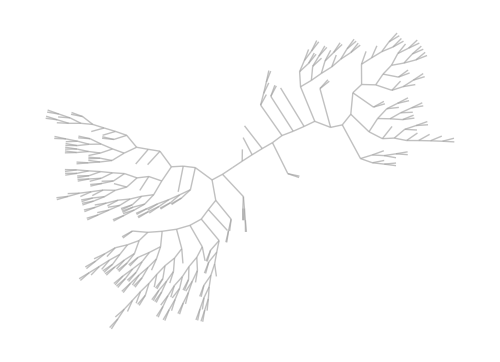

```mathematica
ClusteringTree[datAmpF,GraphLayout->"RadialEmbedding", ClusterDissimilarityFunction->"Average",ImageSize->500]
```

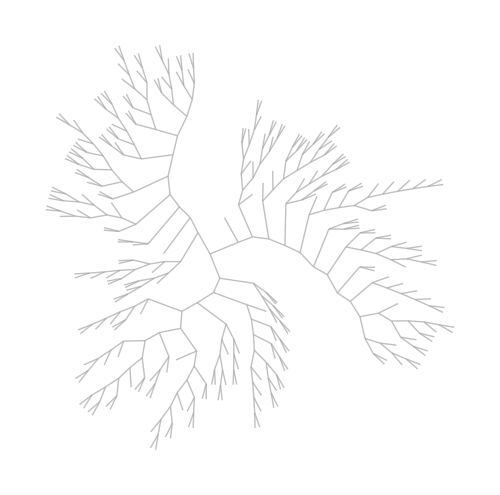

```mathematica
dat1KanaF=(#[[1]]-> #[[2]]&)/@Partition[Riffle[coKana,Table[colorCoF,{80}]],{2}];
dat2KanaF=(#[[1]]-> #[[2]]&)/@Partition[Riffle[trpKana,Table[colorTRPF,{80}]],{2}];
dat3KanaF=(#[[1]]-> #[[2]]&)/@Partition[Riffle[tyrKana,Table[colorTYRF,{80}]],{2}];
datKanaF=Join[dat1KanaF,dat2KanaF,dat3KanaF];

ClusteringTree[datKanaF,GraphLayout->"RadialEmbedding", ClusterDissimilarityFunction->"Average",ImageSize->500]
```

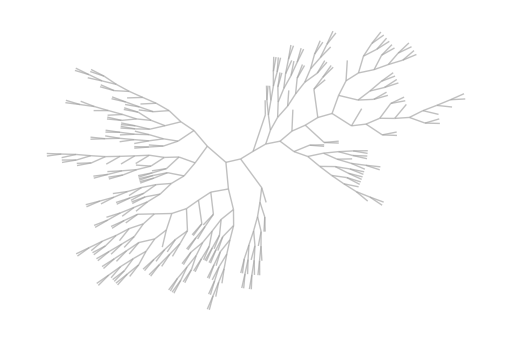

```mathematica
dat1ChlorF=(#[[1]]-> #[[2]]&)/@Partition[Riffle[coChlor,Table[colorCoF,{80}]],{2}];
dat2ChlorF=(#[[1]]-> #[[2]]&)/@Partition[Riffle[trpChlor,Table[colorTRPF,{80}]],{2}];
dat3ChlorF=(#[[1]]-> #[[2]]&)/@Partition[Riffle[tyrChlor,Table[colorTYRF,{80}]],{2}];
datChlorF=Join[dat1ChlorF,dat2ChlorF,dat3ChlorF];

ClusteringTree[datChlorF,GraphLayout->"RadialEmbedding", ClusterDissimilarityFunction->"Average",ImageSize->500]
```

```mathematica
Export["/Users/leo/Desktop/tree.pdf",ClusteringTree[datChlorF,GraphLayout->"RadialEmbedding", ClusterDissimilarityFunction->"Average",ImageSize->500]]
```

/Users/leo/Desktop/tree.pdf

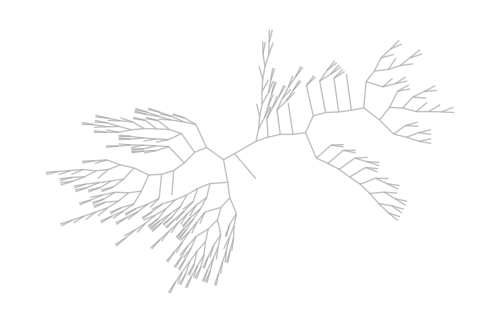

```mathematica
dat1TetraF=(#[[1]]-> #[[2]]&)/@Partition[Riffle[coTetra,Table[colorCoF,{80}]],{2}];
dat2TetraF=(#[[1]]-> #[[2]]&)/@Partition[Riffle[trpTetra,Table[colorTRPF,{80}]],{2}];
dat3TetraF=(#[[1]]-> #[[2]]&)/@Partition[Riffle[tyrTetra,Table[colorTYRF,{80}]],{2}];
datTetraF=Join[dat1TetraF,dat2TetraF,dat3TetraF];

ClusteringTree[datTetraF,GraphLayout->"RadialEmbedding", ClusterDissimilarityFunction->"Average",ImageSize->500]
```

## Survival Analysis

```mathematica
(*Amp*)
```

```mathematica
coAmpSA={80,80,80,80,80,80,77,1,1,0,0,0,0,0,0};
trpAmpSA={80,80,80,80,80,80,80,80,80,80,80,80,80,80,78};
tyrAmpSA={80,80,80,80,80,80,3,3,3,2,2,2,2,2,2};
```

```mathematica
ConstantArray[15,2]
```

{15,15}

```mathematica
ConstantArray[7,3]
```

{7,7,7}

```mathematica
ConstantArray[8,76]
```

{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}

```mathematica
{9}
```

```mathematica
ConstantArray[10,1]
```

{10}

```mathematica
Join[ConstantArray[7,3],ConstantArray[8,76],{10}]
```

{7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,10}

```mathematica
Length[%]
```

80

```mathematica
ConstantArray[0,80]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
coAmpSAEvent=EventData[Join[ConstantArray[7,3],ConstantArray[8,76],{10}],ConstantArray[0,80]];
```

```mathematica
suvCoAmp=SurvivalModelFit[coAmpSAEvent]
```

SurvivalModel[…]

```mathematica
Normal[suvCoAmp][x]//PiecewiseExpand
```

Piecewise[{{0., x==10}, {0.0125, 8≤x<10}, {0.9625, 7≤x<8}, {1., x<7}, {0, True}}]

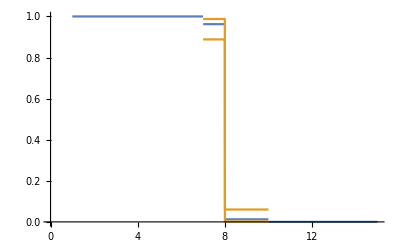

```mathematica
Plot[{suvCoAmp[x],suvCoAmp["PointwiseBands"][x]},{x,1,15},PlotRange-> {0,1}]
```

```mathematica
suvCoAmp["EventTable"]
```

t | SF | Error | Lower 95% | Upper 95%
7 | 0.9625 | 0.0212408 | 0.888238 | 0.987749
8 | 0.0125 | 0.0124216 | 0.00107603 | 0.0602291
10 | 0. | Indeterminate | Indeterminate | Indeterminate

```mathematica
suvCoAmp["FullEventTable"]
```

t | AtRisk | Events | SF | Error | Lower 95% | Upper 95%
7 | 80 | 3 | 0.9625 | 0.0212408 | 0.888238 | 0.987749
8 | 77 | 76 | 0.0125 | 0.0124216 | 0.00107603 | 0.0602291
10 | 1 | 1 | 0. | Indeterminate | Indeterminate | Indeterminate

```mathematica
coAmpSAEvent=EventData[Join[ConstantArray[7,3],ConstantArray[8,76],{10}],ConstantArray[0,80]];
suvCoAmp=SurvivalModelFit[coAmpSAEvent];
Plot[{suvCoAmp[x],suvCoAmp["PointwiseBands"][x]},{x,1,15},PlotRange-> {0,1}]
suvCoAmp["FullEventTable"]
```

```mathematica
Join[ConstantArray[0,2],ConstantArray[1,78]]
```

{0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
{ConstantArray[15,80],Join[ConstantArray[0,2],ConstantArray[1,78]]}
```

{{15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15},{0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
Length[%]
```

80

```mathematica
trpAmpSAEvent=EventData[ConstantArray[15,80],Join[ConstantArray[0,2],ConstantArray[1,78]]]
```

EventData[…]

```mathematica
trpAmpSAEvent=EventData[Join[ConstantArray[15,2],ConstantArray[16,78]],Join[ConstantArray[0,2],ConstantArray[1,78]]]
```

EventData[…]

```mathematica
suvTrpAmp=SurvivalModelFit[trpAmpSAEvent]
```

SurvivalModel[…]

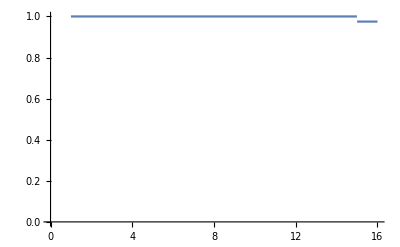

```mathematica
Plot[{suvTrpAmp[x],suvTrpAmp["PointwiseBands"][x]},{x,1,16},PlotRange-> {0,1}]
```

```mathematica
suvTrpAmp["FullEventTable"]
```

SurvivalModel::sclvrng: The confidence range All does not contain any values in the data.

Transpose::nmtx: The first two levels of {{80},«5»} cannot be transposed.

Join::headsd: Expression Transpose[{{80},«5»}] at position 2 is expected to have head List for all expressions at level 2.

Join::headsd: Expression Transpose[{{80},«5»}] at position 3 is expected to have head List for all expressions at level 2.

Grid[Join[{{t,AtRisk,Events,SF,Error,Lower 95%,Upper 95%}},{{15}},Transpose[{{80},{2},{0.975},{0.0174553},SurvivalModel[…][{LowerPointwiseBand,SurvivalFunction}][{15}],SurvivalModel[…][{UpperPointwiseBand,SurvivalFunction}][{15}]}],2],Alignment→{Left,Automatic},Dividers→{{2→GrayLevel[0.7]},{2→GrayLevel[0.7]}},Spacings→Automatic]

```mathematica
trpAmpSAEvent=EventData[Join[ConstantArray[15,2],ConstantArray[16,78]],Join[ConstantArray[0,2],ConstantArray[1,78]]];
suvTrpAmp=SurvivalModelFit[trpAmpSAEvent];
Plot[{suvTrpAmp[x],suvTrpAmp["PointwiseBands"][x]},{x,1,16},PlotRange-> {0,1}]
(*suvTrpAmp["FullEventTable"];*)
```

-Graphics-

```mathematica
coAmpSAEvent
```

```mathematica
trpAmpSAEvent
```

```mathematica
LogRankTest[{coAmpSAEvent,trpAmpSAEvent},"Equal","TestDataTable"]
```

| Statistic | P-Value
Log-Rank | 160.023 | 1.11826×10^-36

```mathematica
LogRankTest[{coAmpSAEvent,trpAmpSAEvent},"Equal","DegreesOfFreedom"]
```

1

```mathematica
{80,80,80,80,80,80,3,3,3,2,2,2,2,2,2}
```

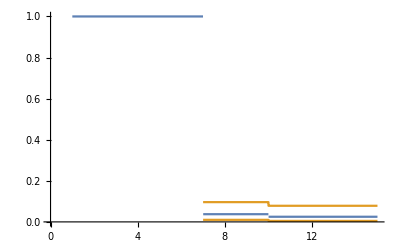

t | SF | Error | Lower 95% | Upper 95%
7 | 0.0375 | 0.0212408 | 0.0100084 | 0.096188
10 | 0.025 | 0.0174553 | 0.00476856 | 0.0784291

```mathematica
tyrAmpSAEvent=EventData[Join[ConstantArray[7,77],ConstantArray[10,1],ConstantArray[15,2]],Join[ConstantArray[0,77],ConstantArray[0,1],ConstantArray[1,2]]];
suvTyrAmp=SurvivalModelFit[tyrAmpSAEvent];
Plot[{suvTyrAmp[x],suvTyrAmp["PointwiseBands"][x]},{x,1,15},PlotRange-> {0,1}]
suvTyrAmp["EventTable"]
```

```mathematica
(******)
```

```mathematica
LogRankTest[{coAmpSAEvent,trpAmpSAEvent},"Equal","TestDataTable"]
```

| Statistic | P-Value
Log-Rank | 160.023 | 1.11826×10^-36

```mathematica
LogRankTest[{coAmpSAEvent,tyrAmpSAEvent},"Equal","TestDataTable"]
```

| Statistic | P-Value
Log-Rank | 108.338 | 2.26671×10^-25

```mathematica
LogRankTest[{trpAmpSAEvent,tyrAmpSAEvent},"Equal","TestDataTable"]
```

| Statistic | P-Value
Log-Rank | 153.352 | 3.20835×10^-35

```mathematica
(*CHLOR*)
```

```mathematica
coChlorSA={80,80,80,80,80,80,80,51,50,50,50,50,50,50,50};
trpChlorSA={80,80,80,80,80,80,80,80,80,80,80,80,80,80,80};
tyrChlorSA={80,80,80,80,80,80,80,80,80,80,80,80,80,80,80};
```

```mathematica
{80,80,80,80,80,80,80,51,50,50,50,50,50,50,50}
```

```mathematica
80-51
```

29

```mathematica
ConstantArray[8,29]
```

{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}

```mathematica
ConstantArray[9,1]
```

{9}

```mathematica
ConstantArray[15,20]
```

{15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15}

```mathematica
Join[ConstantArray[8,29],ConstantArray[9,1],ConstantArray[15,50]]
```

{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15}

```mathematica
Length[%]
```

80

```mathematica
ConstantArray[0,29]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ConstantArray[0,1]
```

{0}

```mathematica
ConstantArray[1,50]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Join[ConstantArray[0,29],ConstantArray[0,1],ConstantArray[1,50]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Length[%]
```

80

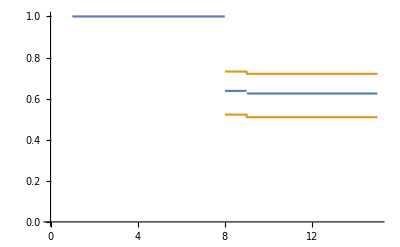

t | AtRisk | Events | SF | Error | Lower 95% | Upper 95%
8 | 80 | 29 | 0.6375 | 0.0537464 | 0.522127 | 0.732061
9 | 51 | 1 | 0.625 | 0.0541266 | 0.509442 | 0.720697

```mathematica
coChlorSAEvent=EventData[Join[ConstantArray[8,29],ConstantArray[9,1],ConstantArray[15,50]],Join[ConstantArray[0,29],ConstantArray[0,1],ConstantArray[1,50]]];
suvCoChlor=SurvivalModelFit[coChlorSAEvent];
Plot[{suvCoChlor[x],suvCoChlor["PointwiseBands"][x]},{x,1,15},PlotRange-> {0,1}]
suvCoChlor["FullEventTable"]
```

```mathematica
ConstantArray[15,80]
```

{15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15}

```mathematica
ConstantArray[1,80]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
trpChlorSAEvent=EventData[ConstantArray[15,80],ConstantArray[1,80]];
```

```mathematica
tyrChlorSAEvent=EventData[ConstantArray[15,80],ConstantArray[1,80]];
```

```mathematica
(******)
```

```mathematica
LogRankTest[{coChlorSAEvent,trpChlorSAEvent},"Equal","TestDataTable"]
```

| Statistic | P-Value
Log-Rank | 36.7625 | 1.33429×10^-9

```mathematica
LogRankTest[{coChlorSAEvent,tyrChlorSAEvent},"Equal","TestDataTable"]
```

| Statistic | P-Value
Log-Rank | 36.7625 | 1.33429×10^-9

```mathematica
LogRankTest[{trpChlorSAEvent,tyrChlorSAEvent},"Equal","TestDataTable"]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

| Statistic | P-Value
Log-Rank | Indeterminate | Indeterminate

```mathematica
(*KANA*)
```

```mathematica
coKanaSA={80,80,80,80,80,60,0,0,0,0,0,0,0,0,0};
trpKanaSA={80,80,80,80,80,80,78,62,59,57,54,52,49,49,49};
tyrKanaSA={80,80,80,80,80,80,68,54,51,49,47,43,42,42,42};
```

```mathematica
{80,80,80,80,80,60,0,0,0,0,0,0,0,0,0}
```

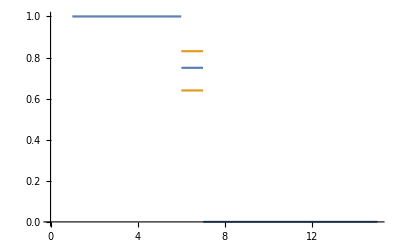

t | AtRisk | Events | SF | Error | Lower 95% | Upper 95%
6 | 80 | 20 | 0.75 | 0.0484123 | 0.639809 | 0.830839
7 | 60 | 60 | 0. | Indeterminate | Indeterminate | Indeterminate

```mathematica
coKanaSAEvent=EventData[Join[ConstantArray[6,20],ConstantArray[7,60]],ConstantArray[0,80]];
suvCoKana=SurvivalModelFit[coKanaSAEvent];
Plot[{suvCoKana[x],suvCoKana["PointwiseBands"][x]},{x,1,15},PlotRange-> {0,1}]
suvCoKana["FullEventTable"]
```

```mathematica
{80,80,80,80,80,80,78,62,59,57,54,52,49,49,49}
```

```mathematica
ConstantArray[7,2]
```

{7,7}

```mathematica
78-62
```

16

```mathematica
ConstantArray[8,16]
```

{8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}

```mathematica
62-59
```

3

```mathematica
ConstantArray[9,3]
```

{9,9,9}

```mathematica
59-57
```

2

```mathematica
ConstantArray[10,2]
```

{10,10}

```mathematica
57-54
```

3

```mathematica
ConstantArray[11,3]
```

{11,11,11}

```mathematica
54-52
```

2

```mathematica
ConstantArray[12,2]
```

{12,12}

```mathematica
52-49
```

3

```mathematica
ConstantArray[13,3]
```

{13,13,13}

```mathematica
Join[ConstantArray[7,2],ConstantArray[8,16],ConstantArray[9,3],ConstantArray[10,2],ConstantArray[11,3],ConstantArray[12,2],ConstantArray[13,3]]
```

{7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,10,10,11,11,11,12,12,13,13,13}

```mathematica
Length[%]
```

31

```mathematica
80-31
```

49

```mathematica
evTrpKana=Join[ConstantArray[7,2],ConstantArray[8,16],ConstantArray[9,3],ConstantArray[10,2],ConstantArray[11,3],ConstantArray[12,2],ConstantArray[13,3],ConstantArray[15,49]]
```

{7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,10,10,11,11,11,12,12,13,13,13,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15}

```mathematica
Length[%]
```

80

```mathematica
zoTrpKana=Join[ConstantArray[0,31],ConstantArray[1,49]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Length[%]
```

80

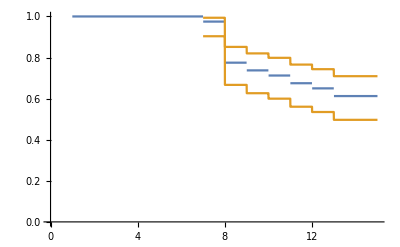

t | AtRisk | Events | SF | Error | Lower 95% | Upper 95%
7 | 80 | 2 | 0.975 | 0.0174553 | 0.90372 | 0.993688
8 | 78 | 16 | 0.775 | 0.0466871 | 0.66693 | 0.85181
9 | 62 | 3 | 0.7375 | 0.0491927 | 0.626394 | 0.820205
10 | 59 | 2 | 0.7125 | 0.0506018 | 0.599835 | 0.798662
11 | 57 | 3 | 0.675 | 0.0523659 | 0.560629 | 0.765712
12 | 54 | 2 | 0.65 | 0.0533268 | 0.534886 | 0.743352
13 | 52 | 3 | 0.6125 | 0.0544683 | 0.496828 | 0.709263

```mathematica
trpKanaSAEvent=EventData[evTrpKana,zoTrpKana];
suvTrpKana=SurvivalModelFit[trpKanaSAEvent];
Plot[{suvTrpKana[x],suvTrpKana["PointwiseBands"][x]},{x,1,15},PlotRange-> {0,1}]
suvTrpKana["FullEventTable"]
```

```mathematica
(* tyr *)
```

```mathematica
{80,80,80,80,80,80,68,54,51,49,47,43,42,42,42}
```

```mathematica
80-68
```

12

```mathematica
ConstantArray[7,12]
```

{7,7,7,7,7,7,7,7,7,7,7,7}

```mathematica
68-54
```

14

```mathematica
ConstantArray[8,14]
```

{8,8,8,8,8,8,8,8,8,8,8,8,8,8}

```mathematica
54-51
```

3

```mathematica
ConstantArray[9,3]
```

{9,9,9}

```mathematica
51-49
```

2

```mathematica
ConstantArray[10,2]
```

{10,10}

```mathematica
49-47
```

2

```mathematica
ConstantArray[11,2]
```

{11,11}

```mathematica
47-43
```

4

```mathematica
ConstantArray[12,4]
```

{12,12,12,12}

```mathematica
43-42
```

1

```mathematica
ConstantArray[13,1]
```

{13}

```mathematica
Join[ConstantArray[7,12],ConstantArray[8,14],ConstantArray[9,3],ConstantArray[10,2],ConstantArray[11,2],ConstantArray[12,4],ConstantArray[13,1]]
```

{7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,10,10,11,11,12,12,12,12,13}

```mathematica
Length[%]
```

38

```mathematica
80-38
```

42

```mathematica
ConstantArray[15,42]
```

{15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15}

```mathematica
Join[ConstantArray[7,12],ConstantArray[8,14],ConstantArray[9,3],ConstantArray[10,2],ConstantArray[11,2],ConstantArray[12,4],ConstantArray[13,1],ConstantArray[15,42]]
```

{7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,10,10,11,11,12,12,12,12,13,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15}

```mathematica
Join[ConstantArray[0,38],ConstantArray[1,42]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Length[%]
```

80

```mathematica
evTyrKana=Join[ConstantArray[7,12],ConstantArray[8,14],ConstantArray[9,3],ConstantArray[10,2],ConstantArray[11,2],ConstantArray[12,4],ConstantArray[13,1],ConstantArray[15,42]];
zoTyrKana=Join[ConstantArray[0,38],ConstantArray[1,42]];
```

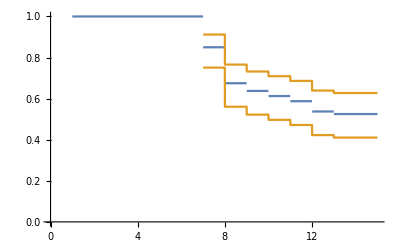

t | AtRisk | Events | SF | Error | Lower 95% | Upper 95%
7 | 80 | 12 | 0.85 | 0.0399218 | 0.751001 | 0.911888
8 | 68 | 14 | 0.675 | 0.0523659 | 0.560629 | 0.765712
9 | 54 | 3 | 0.6375 | 0.0537464 | 0.522127 | 0.732061
10 | 51 | 2 | 0.6125 | 0.0544683 | 0.496828 | 0.709263
11 | 49 | 2 | 0.5875 | 0.055039 | 0.471812 | 0.686188
12 | 47 | 4 | 0.5375 | 0.0557443 | 0.422603 | 0.639236
13 | 43 | 1 | 0.525 | 0.0558318 | 0.41047 | 0.627335

```mathematica
tyrKanaSAEvent=EventData[evTyrKana,zoTyrKana];
suvTyrKana=SurvivalModelFit[tyrKanaSAEvent];
Plot[{suvTyrKana[x],suvTyrKana["PointwiseBands"][x]},{x,1,15},PlotRange-> {0,1}]
suvTyrKana["FullEventTable"]
```

```mathematica
(******)
```

```mathematica
LogRankTest[{coKanaSAEvent,trpKanaSAEvent},"Equal","TestDataTable"]
```

| Statistic | P-Value
Log-Rank | 145.946 | 1.33384×10^-33

```mathematica
LogRankTest[{coKanaSAEvent,tyrKanaSAEvent},"Equal","TestDataTable"]
```

| Statistic | P-Value
Log-Rank | 117.6 | 2.12095×10^-27

```mathematica
LogRankTest[{trpKanaSAEvent,tyrKanaSAEvent},"Equal","TestDataTable"]
```

| Statistic | P-Value
Log-Rank | 1.97143 | 0.160296

```mathematica
(*TETRA*)
```

```mathematica
coTetraSA={80,80,80,80,80,80,80,80,79,67,48,39,34,33,33};
trpTetraSA={80,80,80,80,80,80,80,80,80,80,80,80,80,80,80};
tyrTetraSA={80,80,80,80,80,80,80,80,80,80,80,80,80,80,80};
```

```mathematica
ConstantArray[9,1]
```

{9}

```mathematica
79-67
```

12

```mathematica
ConstantArray[10,12]
```

{10,10,10,10,10,10,10,10,10,10,10,10}

```mathematica
67-48
```

19

```mathematica
ConstantArray[11,19]
```

{11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11}

```mathematica
48-39
```

9

```mathematica
ConstantArray[12,9]
```

{12,12,12,12,12,12,12,12,12}

```mathematica
39-34
```

5

```mathematica
ConstantArray[13,5]
```

{13,13,13,13,13}

```mathematica
34-33
```

1

```mathematica
ConstantArray[14,1]
```

{14}

```mathematica
Join[ConstantArray[9,1],ConstantArray[10,12],ConstantArray[11,19],ConstantArray[12,9],ConstantArray[13,5],ConstantArray[14,1]]
```

{9,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,13,13,13,13,13,14}

```mathematica
Length[%]
```

47

```mathematica
80-47
```

33

```mathematica
ConstantArray[15,33]
```

{15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15}

```mathematica
(**)
```

```mathematica
Join[ConstantArray[9,1],ConstantArray[10,12],ConstantArray[11,19],ConstantArray[12,9],ConstantArray[13,5],ConstantArray[14,1],ConstantArray[15,33]]
```

{9,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,13,13,13,13,13,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15}

```mathematica
Join[ConstantArray[0,47],ConstantArray[1,33]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
evCoTetra=Join[ConstantArray[9,1],ConstantArray[10,12],ConstantArray[11,19],ConstantArray[12,9],ConstantArray[13,5],ConstantArray[14,1],ConstantArray[15,33]];
zoCoTetra=Join[ConstantArray[0,47],ConstantArray[1,33]];
```

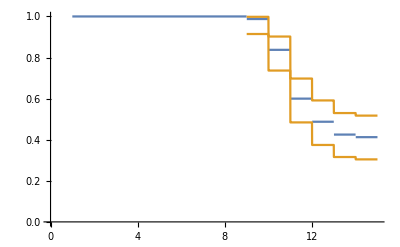

t | AtRisk | Events | SF | Error | Lower 95% | Upper 95%
9 | 80 | 1 | 0.9875 | 0.0124216 | 0.914572 | 0.99823
10 | 79 | 12 | 0.8375 | 0.0412453 | 0.736666 | 0.90222
11 | 67 | 19 | 0.6 | 0.0547723 | 0.484285 | 0.697759
12 | 48 | 9 | 0.4875 | 0.0558842 | 0.37447 | 0.591245
13 | 39 | 5 | 0.425 | 0.0552692 | 0.315821 | 0.529808
14 | 34 | 1 | 0.4125 | 0.055039 | 0.304298 | 0.517325

```mathematica
coTetraSAEvent=EventData[evCoTetra,zoCoTetra];
suvCoTetra=SurvivalModelFit[coTetraSAEvent];
Plot[{suvCoTetra[x],suvCoTetra["PointwiseBands"][x]},{x,1,15},PlotRange-> {0,1}]
suvCoTetra["FullEventTable"]
```

```mathematica
evTrpTetra=ConstantArray[15,80]
```

{15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15}

```mathematica
zoTrpTetra=ConstantArray[1,80]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
trpTetraSAEvent=EventData[evTrpTetra,zoTrpTetra];
```

```mathematica
LogRankTest[{coTetraSAEvent,trpTetraSAEvent},"Equal","TestDataTable"]
```

| Statistic | P-Value
Log-Rank | 67.7115 | 1.89259×10^-16

```mathematica
{coKanaSA,tyrKanaSA}
```

{{80,80,80,80,80,60,0,0,0,0,0,0,0,0,0},{80,80,80,80,80,80,68,54,51,49,47,43,42,42,42}}

```mathematica
Join[ConstantArray[6,20],ConstantArray[7,60]]
```

{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7}

```mathematica
Length[%]
```

80

```mathematica
80-68
```

12

```mathematica
68-54
```

14

```mathematica
54-51
```

3

```mathematica
51-49
```

2

```mathematica
49-47
```

2

```mathematica
47-43
```

4

```mathematica
43-42
```

1

```mathematica
Join[ConstantArray[7,12],ConstantArray[8,14],ConstantArray[9,3],ConstantArray[10,2],ConstantArray[11,2],ConstantArray[12,4],ConstantArray[13,1]]
```

{7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,10,10,11,11,12,12,12,12,13}

```mathematica
Length[%]
```

38

```mathematica
80-38
```

42

```mathematica
Join[ConstantArray[7,12],ConstantArray[8,14],ConstantArray[9,3],ConstantArray[10,2],ConstantArray[11,2],ConstantArray[12,4],ConstantArray[13,1],ConstantArray[13,42]]
```

{7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,10,10,11,11,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13}

```mathematica
Join[ConstantArray[0,38],ConstantArray[1,42]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
(**)
```

```mathematica
ConstantArray[0,80]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7}
```

```mathematica
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
```

```mathematica
{7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,10,10,11,11,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13}
```

```mathematica
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}
```

```mathematica
ev1=EventData[{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}];
```

```mathematica
ev2=EventData[{7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,10,10,11,11,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}];
```

```mathematica
LogRankTest[{ev1,ev2},"TestDataTable"]
```

LogRankTest[{EventData[…],EventData[…]},TestDataTable]

```mathematica
LogRankTest[{ev1,ev2},"Gehan","TestDataTable"]
```

| Statistic | P-Value
Log-Rank | 114.497 | 1.01416×10^-26

```mathematica
LogRankTest[{ev1,ev2},"AndersenPeto","TestDataTable"]
```

| Statistic | P-Value
Log-Rank | 90.9576 | 1.46786×10^-21

```mathematica
LogRankTest[{ev1,ev2},"Equal","TestDataTable"]
```

| Statistic | P-Value
Log-Rank | 117.6 | 2.12095×10^-27

```mathematica
LogRankTest[{ev1,ev2},"Equal","TestStatistic"]
```

117.6

```mathematica
LogRankTest[{ev1,ev2},"Equal","PValue"]
```

2.12095×10^-27

```mathematica
LogRankTest[{ev1,ev2},"Equal","DegreesOfFreedom"]
```

1

Log-Rank Test |  | 
χ^2 | p-value | d.o.f
14.6039 | 0.747417 | 19

```mathematica
LogRankTest[{ev1,ev2},"Peto","TestDataTable"]
```

| Statistic | P-Value
Log-Rank | 91.0009 | 1.43606×10^-21

```mathematica
LogRankTest[{ev1,ev2},"TaroneWare","TestDataTable"]
```

| Statistic | P-Value
Log-Rank | 116.177 | 4.34621×10^-27

```mathematica
suv=SurvivalModelFit[ev2]
```

SurvivalModel[…]

```mathematica
suv[8]
```

0.675

```mathematica
Normal[suv][x]//PiecewiseExpand
```

Piecewise[{{0.525, x==13}, {0.5375, 12≤x<13}, {0.5875, 11≤x<12}, {0.6125, 10≤x<11}, {0.6375, 9≤x<10}, {0.675, 8≤x<9}, {0.85, 7≤x<8}, {1., x<7}, {Indeterminate, True}}]

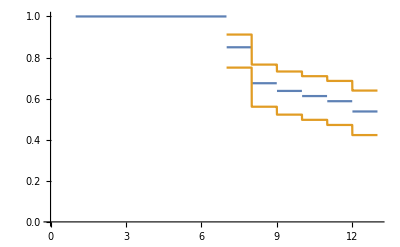

```mathematica
Plot[{suv[x],suv["PointwiseBands"][x]},{x,1,15},PlotRange-> {0,1}]
```

```mathematica
suv["EventTable"]
```

t | SF | Error | Lower 95% | Upper 95%
7 | 0.85 | 0.0399218 | 0.751001 | 0.911888
8 | 0.675 | 0.0523659 | 0.560629 | 0.765712
9 | 0.6375 | 0.0537464 | 0.522127 | 0.732061
10 | 0.6125 | 0.0544683 | 0.496828 | 0.709263
11 | 0.5875 | 0.055039 | 0.471812 | 0.686188
12 | 0.5375 | 0.0557443 | 0.422603 | 0.639236
13 | 0.525 | 0.0558318 | 0.41047 | 0.627335

Tabulate a summary of the estimated SurvivalFunctionpaclet:ref/SurvivalFunction:

```mathematica
suv["FullEventTable"]
```

t | AtRisk | Events | Right | SF | Error | Lower 95% | Upper 95%
7 | 80 | 12 | 0 | 0.85 | 0.0399218 | 0.751001 | 0.911888
8 | 68 | 14 | 0 | 0.675 | 0.0523659 | 0.560629 | 0.765712
9 | 54 | 3 | 0 | 0.6375 | 0.0537464 | 0.522127 | 0.732061
10 | 51 | 2 | 0 | 0.6125 | 0.0544683 | 0.496828 | 0.709263
11 | 49 | 2 | 0 | 0.5875 | 0.055039 | 0.471812 | 0.686188
12 | 47 | 4 | 0 | 0.5375 | 0.0557443 | 0.422603 | 0.639236
13 | 43 | 1 | 42 | 0.525 | 0.0558318 | 0.41047 | 0.627335

```mathematica
LogRankTest[{coKanaSA,trpKanaSA},{1,0},"TestDataTable",Method-> "Permutation"]
```

| Statistic | P-Value
Log-Rank | 3.97289 | 0.05

```mathematica
LogRankTest[{coKanaSA,trpKanaSA},{1,0},"TestDataTable",Method-> "Permutation"]
```

| Statistic | P-Value
Log-Rank | 3.97289 | 0.037

```mathematica
LogRankTest[{coKanaSA,trpKanaSA},{1,0},"TestDataTable",Method-> {"Permutation","MaxSamples"->600}]
```

| Statistic | P-Value
Log-Rank | 3.97289 | 0.045

```mathematica
(*co-tyr permutation*)
```

```mathematica
LogRankTest[{coKanaSA,tyrKanaSA},{1,0},"TestDataTable",Method-> "Permutation"]
```

| Statistic | P-Value
Log-Rank | 3.79653 | 0.044

```mathematica
LogRankTest[{coKanaSA,tyrKanaSA},{1,0},"TestDataTable",Method-> "Permutation"]
```

| Statistic | P-Value
Log-Rank | 3.79653 | 0.057

```mathematica
LogRankTest[{coKanaSA,tyrKanaSA},{1,0},"TestDataTable",Method-> "Permutation"]
```

| Statistic | P-Value
Log-Rank | 3.79653 | 0.043

Use Fleming–Harrington weights:

```mathematica
ρ=1;γ=0;
```

```mathematica
LogRankTest[{e1,e2},{ρ,γ},"TestDataTable"]
```

| Statistic | P-Value
Log-Rank | 3.54507 | 0.0597226

Manually set Fleming–Harrington type weights:

```mathematica
e1=EventData[{32,34,28,26,31,25,29,31,28,25},{0,0,0,0,0,0,0,0,0,1}];
e2=EventData[{30,19,28,35,35,29,33,32,31,29},{0,0,1,0,0,1,0,1,0,1}];
```

Fleming–Harrington weights with ρ==0.5 and γ==0:

```mathematica
LogRankTest[{e1,e2},.5]
```

0.0443182

Use fully specified Fleming–Harrington type weights:

```mathematica
e1=EventData[{32,34,28,26,31,25,29,31,28,25},{0,0,0,0,0,0,0,0,0,1}];
e2=EventData[{30,19,28,35,35,29,33,32,31,29},{0,0,1,0,0,1,0,1,0,1}];
```

Fleming–Harrington weights with ρ==0.5 and γ==1:

```mathematica
LogRankTest[{e1,e2},{.5,1}]
```

0.0407176

```mathematica
LogRankTest[{coKanaSA,tyrKanaSA},{1,0},"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
LogRankTest[{coKanaSA,tyrKanaSA},{1,0},"Properties"]
```

{CovarianceMatrix,DegreesOfFreedom,EventTimes,EventWeights,HypothesisTestData,LogRank,Properties,PValue,PValueTable,ShortTestConclusion,TestConclusion,TestData,TestDataTable,TestEntries,TestStatistic,TestStatisticList,TestStatisticTable}

Retrieve properties for custom reporting:

```mathematica
e=BlockRandom[SeedRandom[4];Table[EventData[RandomVariate[PoissonDistribution[30],100],RandomChoice[{.9,.1}->{0,1},100]],{20}]];
```

```mathematica
{t,p,df}=LogRankTest[e,0,{"TestStatistic","PValue","DegreesOfFreedom"}];
```

```mathematica
Grid[{{"Log-Rank Test",SpanFromLeft},{"χ^2","p-value","d.o.f"},{t,p,df}},Frame->All]
```

Log-Rank Test |  | 
χ^2 | p-value | d.o.f
14.6039 | 0.747417 | 19